```mathematica
f[b_] := Sqrt[1+b]*(4(1+alpha)b^2 +(16alpha-8)b +9-3alpha)/((30-18alpha)b +(9-3alpha))

Series[f[b],{b,0,1}]
```

1+((67-65 alpha) b)/(6 (-3+alpha))+O[b]^2

```mathematica
g[b_] =ArcSinh[ Sqrt[b] ]/Sqrt[b]
```

ArcSinh[√b]/(√b)

```mathematica
Series[g[b],{b,0,2}]
```

1-b/6+(3 b^2)/40+O[b]^(5/2)

```mathematica
Integrate[(1+b (Sin[x])^2)^(3/2)Cos[x]^3,x]
```

1/(48 b^(3/2))(3 (1+6 b) ArcSinh[√b Sin[x]]+√b Sin[x] √(1+b Sin[x]^2) (-3+30 b+2 b (-7+6 b) Sin[x]^2-8 b^2 Sin[x]^4))

```mathematica
Sin[x]^3/3+1/5 b Sin[x]^5

Integrate[(1+b (Sin[x])^2)(Cos[x])(Sin[x])^2,x]
```

Sin[x]^3/3+1/5 b Sin[x]^5

```mathematica
Sin[x]^3/3+1/5 b Sin[x]^5

Integrate[(1+b (Cos[x+Pi/2])^2)(Sin[x+Pi/2])^3,x]
```

Sin[x]^3/3+1/5 b Sin[x]^5

(3 Sin[x])/4+1/8 b Sin[x]+1/12 Sin[3 x]-1/48 b Sin[3 x]-1/80 b Sin[5 x]

```mathematica
Expand[(4 (5+b))/15]
```

4/3+(4 b)/15

```mathematica
Integrate[(1+b (Cos[x])^2)^(1/2)(Sin[x])^3((1+a)(1+b(Cos[x]^2))/2-1),{x,0,Pi},Assumptions->b>0]
```

1/(96 √(b^3 (1+b)))(18 √b-6 a √b+2 b^(3/2)+26 a b^(3/2)-8 b^(5/2)+40 a b^(5/2)+8 b^(7/2)+8 a b^(7/2)+9 ⅈ √(1+b) π-3 ⅈ a √(1+b) π+30 ⅈ b √(1+b) π-18 ⅈ a b √(1+b) π+3 ⅈ √(1+b) (-3+a-10 b+6 a b) ArcCsc[1/(√(1+b))]+3 ⅈ √(1+b) (-3+a-10 b+6 a b) ArcSin[√(1+b)])

```mathematica
Integrate[(1+b (Cos[x])^2)^(3/2)(Sin[x])^3,{x,0,Pi},Assumptions->b>0]
```

(-6 √(b (1+b))+32 √(b^3 (1+b))+8 √(b^5 (1+b))+6 (1+6 b) ArcSinh[√b])/(48 b^(3/2))

```mathematica
FullSimplify[(√(1+b) (3+2 b) (1+4 b))/(24 b)-ArcSinh[√b]/(8 b^(3/2))]
```

(√(1+b) (3+2 b) (1+4 b))/(24 b)-ArcSinh[√b]/(8 b^(3/2))

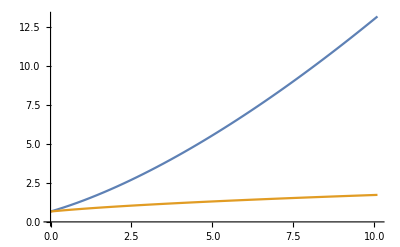

```mathematica
Plot[{(√(1+b) (3+2 b) (1+4 b))/(24 b)-ArcSinh[√b]/(8 b^(3/2)),(√(1+b) (1+2 b))/(4 b)-ArcSinh[√b]/(4 b^(3/2))},{b,0,10.095833086995265}]
```

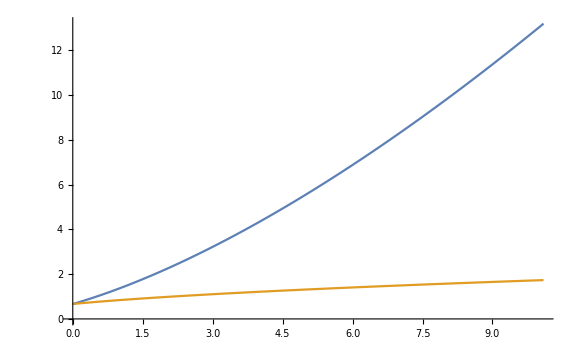

```mathematica
Show[%51,ImageSize->Large]
```

```mathematica
Show[%52,Background->None]
```

-Graphics-

```mathematica
Integrate[Cosh[x]^4,{x,-Arcsinh[Sqrt[b]],Arcsinh[Sqrt[b]]}]
```

1/16 (12 Arcsinh[√b]+8 Sinh[2 Arcsinh[√b]]+Sinh[4 Arcsinh[√b]])

```mathematica
h[b_]:=1/16 (12 Arcsinh[√b]+8 Sinh[2 Arcsinh[√b]]+Sinh[4 Arcsinh[√b]])/(3b Sqrt[b])+2(1+b)^(3/2)/(3 b)
```

```mathematica
h[0.1]
```

7.69126+0.658808 (12 Arcsinh[0.316228]+8 Sinh[2 Arcsinh[0.316228]]+Sinh[4 Arcsinh[0.316228]])

```mathematica
Plot[h[b],{b,1,10.0}]
```

-Graphics-

-Graphics-

```mathematica
Integrate[(1+b (Cos[x])^2)^(1/2)(Sin[x])(Cos[x])^2,{x,0,Pi},Assumptions->b>0]
```

(√(1+b) (1+2 b))/(4 b)-ArcSinh[√b]/(4 b^(3/2))

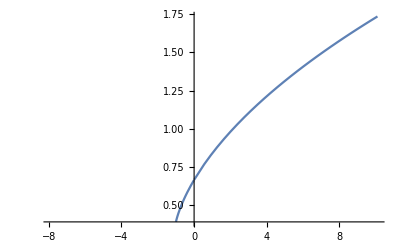

```mathematica
Plot[(√(1+b) (1+2 b))/(4 b)-ArcSinh[√b]/(4 b^(3/2)),{b,-7.904166913004735,10.095833086995265}]
```

```mathematica
const=Table[{0.01,0.99},{i,1,1000}]
```

{{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99},{0.01,0.99}}

```mathematica
const=Range[0.01,0.99,0.01]
f[b_]:=Sqrt[b+1](4(1+const)b^2+(16const-8)b+(9-3const))/((30-18const)b+(9-3const))-ArcSinh[Sqrt[b]]/Sqrt[b]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99}

```mathematica
f[b]
```

{-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.97-7.84 b_+4.04 b_^2))/(8.97+29.82 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.94-7.68 b_+4.08 b_^2))/(8.94+29.64 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.91-7.52 b_+4.12 b_^2))/(8.91+29.46 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.88-7.36 b_+4.16 b_^2))/(8.88+29.28 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.85-7.2 b_+4.2 b_^2))/(8.85+29.1 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.82-7.04 b_+4.24 b_^2))/(8.82+28.92 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.79-6.88 b_+4.28 b_^2))/(8.79+28.74 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.76-6.72 b_+4.32 b_^2))/(8.76+28.56 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.73-6.56 b_+4.36 b_^2))/(8.73+28.38 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.7-6.4 b_+4.4 b_^2))/(8.7+28.2 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.67-6.24 b_+4.44 b_^2))/(8.67+28.02 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.64-6.08 b_+4.48 b_^2))/(8.64+27.84 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.61-5.92 b_+4.52 b_^2))/(8.61+27.66 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.58-5.76 b_+4.56 b_^2))/(8.58+27.48 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.55-5.6 b_+4.6 b_^2))/(8.55+27.3 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.52-5.44 b_+4.64 b_^2))/(8.52+27.12 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.49-5.28 b_+4.68 b_^2))/(8.49+26.94 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.46-5.12 b_+4.72 b_^2))/(8.46+26.76 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.43-4.96 b_+4.76 b_^2))/(8.43+26.58 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.4-4.8 b_+4.8 b_^2))/(8.4+26.4 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.37-4.64 b_+4.84 b_^2))/(8.37+26.22 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.34-4.48 b_+4.88 b_^2))/(8.34+26.04 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.31-4.32 b_+4.92 b_^2))/(8.31+25.86 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.28-4.16 b_+4.96 b_^2))/(8.28+25.68 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.25-4. b_+5. b_^2))/(8.25+25.5 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.22-3.84 b_+5.04 b_^2))/(8.22+25.32 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.19-3.68 b_+5.08 b_^2))/(8.19+25.14 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.16-3.52 b_+5.12 b_^2))/(8.16+24.96 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.13-3.36 b_+5.16 b_^2))/(8.13+24.78 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.1-3.2 b_+5.2 b_^2))/(8.1+24.6 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.07-3.04 b_+5.24 b_^2))/(8.07+24.42 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.04-2.88 b_+5.28 b_^2))/(8.04+24.24 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (8.01-2.72 b_+5.32 b_^2))/(8.01+24.06 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.98-2.56 b_+5.36 b_^2))/(7.98+23.88 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.95-2.4 b_+5.4 b_^2))/(7.95+23.7 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.92-2.24 b_+5.44 b_^2))/(7.92+23.52 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.89-2.08 b_+5.48 b_^2))/(7.89+23.34 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.86-1.92 b_+5.52 b_^2))/(7.86+23.16 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.83-1.76 b_+5.56 b_^2))/(7.83+22.98 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.8-1.6 b_+5.6 b_^2))/(7.8+22.8 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.77-1.44 b_+5.64 b_^2))/(7.77+22.62 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.74-1.28 b_+5.68 b_^2))/(7.74+22.44 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.71-1.12 b_+5.72 b_^2))/(7.71+22.26 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.68-0.96 b_+5.76 b_^2))/(7.68+22.08 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.65-0.8 b_+5.8 b_^2))/(7.65+21.9 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.62-0.64 b_+5.84 b_^2))/(7.62+21.72 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.59-0.48 b_+5.88 b_^2))/(7.59+21.54 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.56-0.32 b_+5.92 b_^2))/(7.56+21.36 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.53-0.16 b_+5.96 b_^2))/(7.53+21.18 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.5+6. b_^2))/(7.5+21. b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.47+0.16 b_+6.04 b_^2))/(7.47+20.82 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.44+0.32 b_+6.08 b_^2))/(7.44+20.64 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.41+0.48 b_+6.12 b_^2))/(7.41+20.46 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.38+0.64 b_+6.16 b_^2))/(7.38+20.28 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.35+0.8 b_+6.2 b_^2))/(7.35+20.1 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.32+0.96 b_+6.24 b_^2))/(7.32+19.92 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.29+1.12 b_+6.28 b_^2))/(7.29+19.74 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.26+1.28 b_+6.32 b_^2))/(7.26+19.56 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.23+1.44 b_+6.36 b_^2))/(7.23+19.38 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.2+1.6 b_+6.4 b_^2))/(7.2+19.2 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.17+1.76 b_+6.44 b_^2))/(7.17+19.02 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.14+1.92 b_+6.48 b_^2))/(7.14+18.84 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.11+2.08 b_+6.52 b_^2))/(7.11+18.66 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.08+2.24 b_+6.56 b_^2))/(7.08+18.48 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.05+2.4 b_+6.6 b_^2))/(7.05+18.3 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (7.02+2.56 b_+6.64 b_^2))/(7.02+18.12 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.99+2.72 b_+6.68 b_^2))/(6.99+17.94 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.96+2.88 b_+6.72 b_^2))/(6.96+17.76 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.93+3.04 b_+6.76 b_^2))/(6.93+17.58 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.9+3.2 b_+6.8 b_^2))/(6.9+17.4 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.87+3.36 b_+6.84 b_^2))/(6.87+17.22 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.84+3.52 b_+6.88 b_^2))/(6.84+17.04 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.81+3.68 b_+6.92 b_^2))/(6.81+16.86 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.78+3.84 b_+6.96 b_^2))/(6.78+16.68 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.75+4. b_+7. b_^2))/(6.75+16.5 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.72+4.16 b_+7.04 b_^2))/(6.72+16.32 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.69+4.32 b_+7.08 b_^2))/(6.69+16.14 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.66+4.48 b_+7.12 b_^2))/(6.66+15.96 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.63+4.64 b_+7.16 b_^2))/(6.63+15.78 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.6+4.8 b_+7.2 b_^2))/(6.6+15.6 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.57+4.96 b_+7.24 b_^2))/(6.57+15.42 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.54+5.12 b_+7.28 b_^2))/(6.54+15.24 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.51+5.28 b_+7.32 b_^2))/(6.51+15.06 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.48+5.44 b_+7.36 b_^2))/(6.48+14.88 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.45+5.6 b_+7.4 b_^2))/(6.45+14.7 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.42+5.76 b_+7.44 b_^2))/(6.42+14.52 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.39+5.92 b_+7.48 b_^2))/(6.39+14.34 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.36+6.08 b_+7.52 b_^2))/(6.36+14.16 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.33+6.24 b_+7.56 b_^2))/(6.33+13.98 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.3+6.4 b_+7.6 b_^2))/(6.3+13.8 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.27+6.56 b_+7.64 b_^2))/(6.27+13.62 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.24+6.72 b_+7.68 b_^2))/(6.24+13.44 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.21+6.88 b_+7.72 b_^2))/(6.21+13.26 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.18+7.04 b_+7.76 b_^2))/(6.18+13.08 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.15+7.2 b_+7.8 b_^2))/(6.15+12.9 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.12+7.36 b_+7.84 b_^2))/(6.12+12.72 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.09+7.52 b_+7.88 b_^2))/(6.09+12.54 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.06+7.68 b_+7.92 b_^2))/(6.06+12.36 b_),-ArcSinh[√b_]/(√b_)+(√(1+b_) (6.03+7.84 b_+7.96 b_^2))/(6.03+12.18 b_)}

```mathematica
roots:=FindRoot[(-ArcSinh[√b]/(√b)+(Sqrt [1+b] *(8.97-7.84 * b +4.04* b^2))/(8.97+29.82* b)),{b,0.1}]
```

```mathematica
roots
```

FindRoot::nlnum: The function value {-0.984042+0.757115 Sqrt} is not a list of numbers with dimensions {1} at {b} = {0.1}.

FindRoot[-ArcSinh[√b]/(√b)+(Sqrt (1+b) (8.97-7.84 b+4.04 b^2))/(8.97+29.82 b),{b,0.1}]

```mathematica
f[b,0]
```

((1+b) (9-8 b+4 b^2) Sqrt)/(9+30 b)-ArcSinh[√b]/(√b)

```mathematica
NSolve[(-ArcSinh[√b]/(√b)+(Sqrt[1+b](8.97-7.84 b +4.04 b^2))/(8.97+29.82 b))==0,b]
```

NSolve[((1+b) (8.97-7.84 b+4.04 b^2) Sqrt)/(8.97+29.82 b)-ArcSinh[√b]/(√b)==0,b]

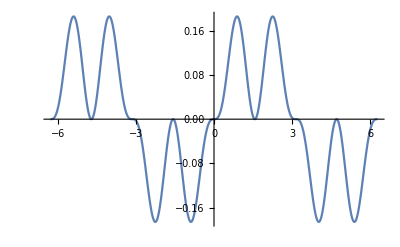

```mathematica
Plot[Sin[x]^3Cos[x]^2, {x,-2 Pi,2 Pi}]
```

```mathematica
Sin[3ArcSin[x]]
```

```mathematica
Sin[5 ArcSin[x]]
```

Sin[5 ArcSin[x]]

```mathematica
TrigExpand[Sin[5 ArcSin[x]]]
```

5 x-20 x^3+16 x^5

```mathematica
FunctionExpand[Sin[3 ArcSin[x]]]
```

3 x-4 x^3

```mathematica
TrigToExp[Sin[3 ArcSin[x]]]
```

1/2 ⅈ (1/((ⅈ x+√(1-x^2))^3)-(ⅈ x+√(1-x^2))^3)

```mathematica
Expand[1/2 ⅈ (1/((ⅈ x+√(1-x^2))^3)-(ⅈ x+√(1-x^2))^3)]
```

(3 x)/2-2 x^3-1/2 ⅈ √(1-x^2)+2 ⅈ x^2 √(1-x^2)+ⅈ/(2 (ⅈ x+√(1-x^2))^3)

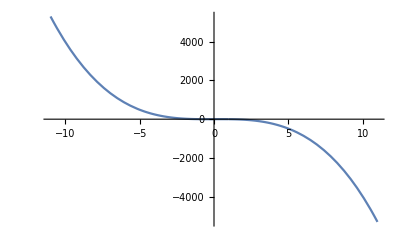

```mathematica
Plot[Sin[3 ArcSin[x]],{x,-11.,11.}]
```

```mathematica
16/80
```

1/5

```mathematica
(1/2-1/12)
```

5/12

```mathematica
1/8-3/60
```

3/40

48

80